## Import

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../src/";
Get[pathSRC<>"basic.m"];
Get[pathSRC<>"dftb.m"];
Get[pathSRC<>"negf.m"];
Get[pathSRC<>"xyz.m"];

Get["../skf/auorg.E.m"];
Get["../skf/auorg.V.mx"];
Get["../skf/auorg.S.mx"];
```

```mathematica
GetOrbitalΣ[Σd_,orbIndex_:"Full"]:=Module[{occm,mo},
bands=(
{atomIndex,σ}=#;
mo=MAXORB[types⟦atomIndex⟧];
If[orbIndex=="Full",occm=IdentityMatrix[mo]];
If[orbIndex=="s",occm=DiagonalMatrix[PadRight[{1},mo]]];
If[orbIndex=="p",occm=DiagonalMatrix[PadRight[{0,1,1,1},mo]]];
If[orbIndex=="d",occm=DiagonalMatrix[PadRight[{0,0,0,0,1,1,1,1,1},mo]]];

Band[{orbInForAtomIn[[atomIndex]],orbInForAtomIn[[atomIndex]]}]->
σ*occm
)&/@Σd;
SparseArray[bands,{norb,norb}]
]
```

```mathematica
?DiagSparseMatrix
```

```mathematica
DiagSparseMatrix[{1},9];
DiagonalMatrix[PadRight[{0,1,1,1},9]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
PadRight[{1},9]//Length
```

9

```mathematica
?Dia
```

## Ham gen

```mathematica
moleName="mcpp_1Au";
{atoms,types,bonds}=ImportXYZ[moleName<>".xyz"];
natom=Length[atoms]
```

68

```mathematica
h=DFTBSolver2[atoms,types];
s=DFTBSolver2[atoms,types,"S"];
```

```mathematica
(*self energy diagonal element: atom index, Im self energy[eV]*)
ΣdL=Table[{i,1},{i,67,67}];
ΣdR=Table[{i,1},{i,68,68}];
(*orbital-atom relation*)
orbInAtom=MAXORB/@types;
norb=Total[MAXORB/@types];
orbInForAtomIn=Accumulate[{1}~Join~orbInAtom][[1;;-2]];
(*self energy diagonal element applied to orbital: orbital index, Im self energy[Hartree]*)
ΣL=-I*0.1*GetOrbitalΣ[ΣdL];
ΣR=-I*0.1*GetOrbitalΣ[ΣdR];

ΣLs=-I*0.1*GetOrbitalΣ[ΣdL,"s"];
ΣRs=-I*0.1*GetOrbitalΣ[ΣdR,"s"];

ΣLp=-I*0.1*GetOrbitalΣ[ΣdL,"p"];
ΣRp=-I*0.1*GetOrbitalΣ[ΣdR,"p"];

ΣLd=-I*0.1*GetOrbitalΣ[ΣdL,"d"];
ΣRd=-I*0.1*GetOrbitalΣ[ΣdR,"d"];
```

```mathematica
ΣLd
```

SparseArray[…]

## MOL

```mathematica
atomsListM=Range[1,68];
atomsM=atoms⟦atomsListM⟧;
typesM=types⟦atomsListM⟧;
hM=DFTBSolver2[atomsM,typesM];
sM=DFTBSolver2[atomsM,typesM,"S"];
{eval,evec}=MyEigensystem[{hM,sM}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atomsM,typesM]
EF
```

{-4.33643,-4.2322,-4.28431,0.104235,107}

-4.28431

```mathematica
(*{eval,evec}=MyEigensystem[{h,s}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atoms,types]
EF*)
```

## Highlight Contact and Molecule

```mathematica
highlightAtom=Table[
{
If[MemberQ[ΣdL⟦All,1⟧,i],clr=Red,
If[MemberQ[ΣdR⟦All,1⟧,i],clr=Blue,
If[MemberQ[atomsListM,i],clr=Orange,
clr=Gray
];
];
];
clr,
Sphere[atoms⟦i⟧]},
{i,natom}
];
Graphics3D[
highlightAtom
]
```

-Graphics3D-

```mathematica
eon["Au.p"]
eon["C.p"]
```

-0.758093

-5.28867

## NEGF run

```mathematica
{emin,emax,estep}={EF-2,EF+2,0.02};
```

```mathematica
et=Table[
{
NEGFSystemWBΣS[ϵ,h,s,ΣL,ΣR]⟦1⟧,
NEGFSystemWBΣS[ϵ,h,s,ΣLs,ΣRs]⟦1⟧,
NEGFSystemWBΣS[ϵ,h,s,ΣLp,ΣRp]⟦1⟧,
NEGFSystemWBΣS[ϵ,h,s,ΣLd,ΣRd]⟦1⟧
},
{ϵ,emin,emax,estep}
];
```

```mathematica
Export["trans.m",et];
```

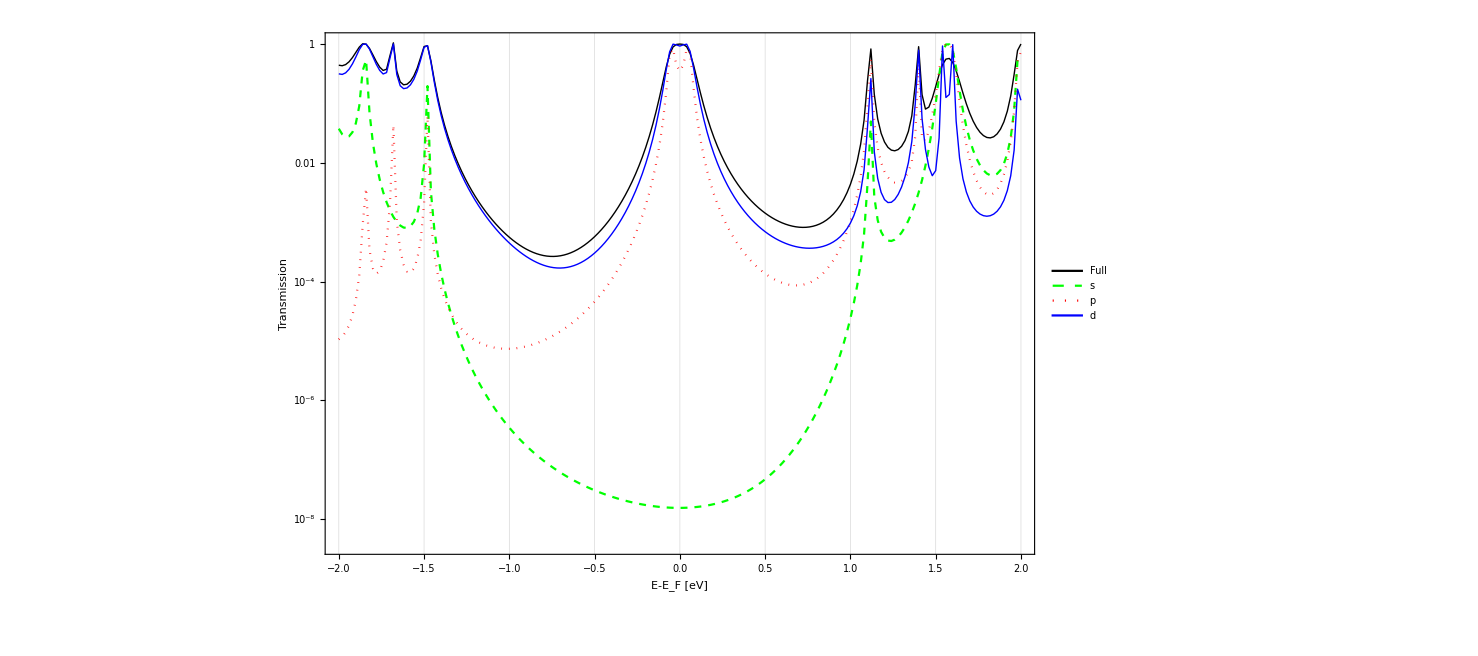

```mathematica
ListLogPlot[et//Transpose,GridLines->{eval-EF,None},
DataRange->{-2,2},
FrameLabel->{"E-E_F [eV]"," Transmission "},
Frame->True,
AspectRatio->0.6,
PlotLegends->Placed[{"Full","s","p","d"},{0.5,0.35}],
Joined->True,
PlotStyle->{{Black,Thick},{Green,Dashed},{Red,Dotted},{Blue,Thin}},
ImageSize->{800,500},
Axes->False,
styles]
```

```mathematica
et1
```

```mathematica
TableForm[
Slater[atoms⟦6⟧-atoms⟦67⟧,types⟦6⟧,types⟦67⟧],
TableHeadings->{{"s","x","y","z"},{"s","x","y","z","d1","d2","d3","d4","d5"}}]
```

| s | x | y | z | d1 | d2 | d3 | d4 | d5
s | -4.20178 | -1.23811 | 3.84354 | 4.12087 | 0.821743 | -2.73504 | 0.881035 | 1.14314 | -0.880195
x | 0.64402 | -1.34577 | -0.657074 | -0.704485 | 0.780693 | 0.8635 | 0.837023 | -0.695964 | 0.471337
y | -1.99926 | -0.657074 | 0.482355 | 2.18697 | 0.470332 | -1.56543 | 0.8635 | 0.0802545 | -1.4632
z | -2.14352 | -0.704485 | 2.18697 | 0.787331 | 0.8635 | -1.83389 | 0.590749 | 1.20123 | 0.362777